```mathematica
t[n_,a_,b_]:=b(Floor[n/b]-Floor[(n-1)/b])-a(Floor[n/a]-Floor[(n-1)/a])
```

```mathematica
Table[ t[n,51,50],{n,1,100}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50,-51,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,50}

```mathematica
Clear[p]
p[n_,k_]:= p[n,k]=(1/2)Sum[ If[t[2 j,3,2]==0,0,t[2 j,3,2](1/k-p[n/j,k+1])],{j,3/2,n,1/2}]
```

```mathematica
p[100,1]
```

-8149753/2365440

```mathematica
binomial[z_,k_]:=binomial[z,k]=Product[z-j,{j,0,k-1}]/k!
Ds[n_,0,s_,a_]:=UnitStep[n-1]
Ds[n_,1,s_,a_]:=Ds[n,1,s,a]=HarmonicNumber[Floor[n],s]-HarmonicNumber[a,s]
Ds[n_,2,s_,a_]:=Ds[n,2,s,a]=Sum[(m^(-2s))+2(m^-s) (Ds[Floor[n/m],1,s,m]),{m,a+1,Floor[n^(1/2)]}]
Ds[n_,k_,s_,a_]:=Ds[n,k,s,a]=Sum[(m^(-s k))+k(m^(-s(k-1))) Ds[Floor[n/(m^(k-1))],1,s,m]+Sum[binomial[k,j] (m^-s)^j Ds[Floor[n/(m^j)],k-j,s,m],{j,1,k-2}],{m,a+1,Floor[n^(1/k)]}]
Dnsz[n_,s_,z_]:=Expand@Sum[binomial[z,k]Ds[n,k,s,1],{k,0,Log2@n}]

Dnsyabz[n_,s_,a_,b_,z_]:=Expand@Sum[(-1)^j binomial[z,j] (a/b)^(j(1-s))Dnsz[n/((a/b)^j),s,z],{j,0,Log[a/b,n]}]
```

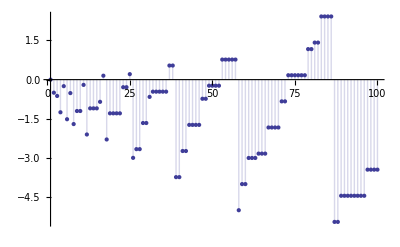

```mathematica
DiscretePlot[D[Dnsyabz[n,0,3,2,z],z]/.z->0,{n,1,100}]
```

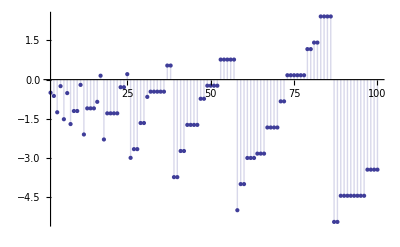

```mathematica
DiscretePlot[p[n,1],{n,2,100}]
```

```mathematica
(**)
```

```mathematica
Clear[da,dc]
da[n_, z_, a_,x_,y_] := da[n,z,a,x,y]=If[n<y,1,da[n,z,a,x,y+x]+If[t[x^-1 y,a,x^-1]==0,0,Sum[ binomial[z,k]x^k t[x^-1 y,a,x^-1]^k da[n/y^k,z-k,a,x,y+x],{k,1,Log[y,n]}]]]
dc[n_, z_, a_,x_,y_] := dc[n,z,a,x,y]=If[n<x y,1,dc[n,z,a,x,y+1]+If[t[y,a,x^-1]==0,0,Sum[ binomial[z,k]x^k t[ y,a,x^-1]^k dc[n/(x y)^k,z-k,a,x,y+1],{k,1,Log[x y,n]}]]]
```

```mathematica
D[da[100,z,3,1/2,1+1/2],z]/.z->0
```

-8149753/2365440

```mathematica
D[dc[100,z,3,1/2,3],z]/.z->0
```

-8149753/2365440

```mathematica
DiscretePlot[D[da[n,z,3,1/2,1+1/2],z]/.z->0,{n,1,100}]
```

-Graphics-

```mathematica
((1/2) t[3/2 (1/2)^-1,3,(1/2)^-1])
```

-3/2

```mathematica
DiscretePlot[D[dc[n,z,3,1/2,3],z]/.z->0,{n,1,100}]
```

-Graphics-

```mathematica
$RecursionLimit = 100000
```

100000

```mathematica
D[da[100,z,81,1/80,2],z]/.z->0
```

-1899762991297/1572864000000